1) Physics 170E Project #1
Nathan Magari
805505312
natemagari@g.ucla.edu

2) Programming Experience

I have experience with Mathematica from the 105A and 105B labs, as well as Python from the Physics 4 labs, C++ from PIC 10A, and JavaScript from AP Computer Science A. I'm also currently using R in my astronomy class. Out of all the programming languages I've used, Mathematica and Python are by far my favorites.

```mathematica
(* 3 *)
Remove["Global`*"]
Print[Style["3) Symbolic Expression Evaluation",16,Bold,Red]]
(* Luckily expressions in Mathematica can be inputed symbolically 
so this looks the same on the assignment pdf or how it would look 
if you wrote it down on scratch paper *)
ans = ((3.9122 10^2)^(1/3)(√(2.017 10^-5)))/(3.661 10^-4);
(* It also lets you print the whole expession nicely along with its approximate numerical value *)
Print["\nThe expression (3.9122 x SuperscriptBox[10, 2])^(1/3)/(3.661 x SuperscriptBox[10, -4]) is approximately equal to ",NumberForm[ans,4]]
```

3) Symbolic Expression Evaluation

The expression (3.9122 x SuperscriptBox[10, 2])^(1/3)/(3.661 x SuperscriptBox[10, -4]) is approximately equal to 89.72

```mathematica
(* 4 *)
Remove["Global`*"]
Print[Style["4) Polynomial Factoring",16,Bold,Red]]
poly = 2 x^4 y^6+ 6 x^2 y^3- 20;
fac = Factor[poly];
Print["Mathematica factors using the Factor[] function:\n\n",poly," = ", fac]
```

4) Polynomial Factoring

Mathematica factors using the Factor[] function:

-20+6 x^2 y^3+2 x^4 y^6 = 2 (-2+x^2 y^3) (5+x^2 y^3)

```mathematica
(* 5 *)
Remove["Global`*"]
Print[Style["5) Trigonometric Identity",16,Bold,Red]]
expr = Sec[θ]Tan[θ](Sec[θ] + Tan[θ]) + (Sec[θ] - Tan[θ]);
Print["The RHS of this equation is obtained from the LHS by tacking on a //FullSimplify:\n\n"expr," = ", expr//FullSimplify]
(* Let's check its work *)
Print[Style["\n** Quick check **",Blue],"\nFrom Sin^2[θ] + Cos^2[θ] = 1:   Sec^2[θ] = Tan^2[θ] + 1   and   Tan^2[θ] = Sec^2[θ] - 1"]
Print["So ",expr,"\n\n= Sec[θ] - Tan[θ] + Tan[θ] Sec^2[θ] + Sec[θ] Tan^2[θ]\n= Sec[θ] - Tan[θ] + Tan[θ](Tan^2[θ] + 1) + Sec[θ](Sec^2[θ] - 1) = ",expr//FullSimplify,"  ",Style["✓",Bold,45,Red]]
```

5) Trigonometric Identity

The RHS of this equation is obtained from the LHS by tacking on a //FullSimplify:

 (Sec[θ]-Tan[θ]+Sec[θ] Tan[θ] (Sec[θ]+Tan[θ])) = Sec[θ]^3+Tan[θ]^3

** Quick check **
From Sin^2[θ] + Cos^2[θ] = 1:   Sec^2[θ] = Tan^2[θ] + 1   and   Tan^2[θ] = Sec^2[θ] - 1

So Sec[θ]-Tan[θ]+Sec[θ] Tan[θ] (Sec[θ]+Tan[θ])

= Sec[θ] - Tan[θ] + Tan[θ] Sec^2[θ] + Sec[θ] Tan^2[θ]
= Sec[θ] - Tan[θ] + Tan[θ](Tan^2[θ] + 1) + Sec[θ](Sec^2[θ] - 1) = Sec[θ]^3+Tan[θ]^3  ✓

6) Loss of Significance (Particle in One Dimension)

i) Roots the old fashioned way

Our position function is x(t) = -500.+5000000000 t-1.5×10^-7 t^2
We want to find the roots of x(t) (times for which x = 0).

The quadratic formula tells us that t = (-b+  ± SqrtBox[SuperscriptBox[b, 2]  -  4  a c])/(2  a)

Using the old fashioned method, we find that
t1 = 0.
t2 = 3.33333×10^16

ii) Trying and not succeeding

The average velocity function is defined as v_(x, ave) = (x (t) - x (0))/(t - 0)
The roots of the function x(t) are in principle non-zero, but because of loss of significance,
v_(x, ave)(t1) = Indeterminate
v_(x, ave)(t2) = 1.5×10^-14

The indeterminate value for the first velocity is because t1 is stored as 0 due to loss of significance.

A plot of the position function quickly reveals the problem:

-Graphics-

Zooming way in...

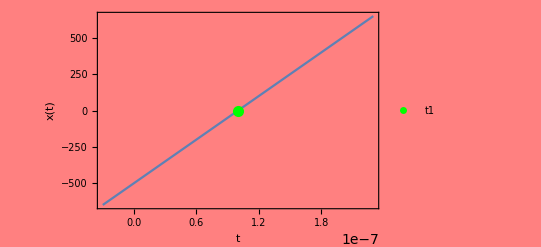

t1 is too small to evaluate using the quadratic formula!

iii) Doing it the right way

Instead of using the quadratic formula directly, let's make it friendlier
t = (-b+  ± SqrtBox[SuperscriptBox[b, 2]  -  4  a c])/(2  a) = (-b/(2  a)) ∓ √((FractionBox[b, 2  a])^2)    (note the ± changes to ∓ because a < 0)

or more succinctly, t = q ∓ √(q^2)
where we have defined q ≡ -b/(2  a) and p ≡ c/a

Using a power series expansion about p = 0:
√(-p+q^2) ≈ -p/(2 √(q^2))+√(q^2) = q - p/(2  q)

So that means 
t1 ≈ p/(2  q) = - c/b = 1.×10^-7  and
 t2 ≈ 2q + c/b ≈ 2q = - b/a = 3.33333×10^16

Using the refined method, we find that
t1 = 1.×10^-7
t2 = 3.33333×10^16

Now the average velocities should not give us any issues:
v_(x, ave)(t1) = 5.×10^9
v_(x, ave)(t2) = 1.5×10^-14

***************************************************************************************
As a final note on the problem, you can 'cheat' and use Mathematica's FindRoot[] function

FindRoot[x[t],{t,0}] evaluates to {t→1.×10^-7}
and FindRoot[x[t],{t,10^17}] evaluates to {t→3.33333×10^16}

But finding the right root isn't always so easy.
For instance, FindRoot[x[t],{t,10^16}] evaluates to {t→1.×10^-7}
giving the root close to zero even though the guess was 10^16.

I want to plot the value of FindRoot[] for different initial guesses and see what happens.

I borrowed and slightly modified this function from the Wolfram website called TwoAxisPlot[]
in order to get both the FindRoot[] output and x[t] on the same plot with scaled axes.

The page is at this url: https://reference.wolfram.com/language/howto/GeneratePlotsWithTwoVerticalScales.html

Here is the plot I made:

-Graphics-

The plot indicates that the root given is determined by which side of the vertex of the parabola you are on.
This makes complete sense since FindRoot[] presumably uses Newton's method.
That's all, folks!

```mathematica
(* 6 *)
Remove["Global`*"]
Print[Style["6) Loss of Significance (Particle in One Dimension)",16,Bold,Red]]
(* Let's define the position function *)
a =-1.5 10^-7;
b = 5 10^9;
c = -500.0;
x[t_] = c + b t +a t^2;
Print[Style["\ni) Roots the old fashioned way",Bold]]
Print["Our position function is x(t) = ", x[t],"\nWe want to find the roots of x(t) (times for which x = 0)."]
(* i *)
(* Let's do it the wrong way first *)
t1 = (-b+√(b^2-4a c))/(2a);
t2  = (-b-√(b^2-4a c))/(2a);
Print["The quadratic formula tells us that t = (-b+  ± SqrtBox[SuperscriptBox[b, 2]  -  4  a c])/(2  a)"]

Print["\nUsing the old fashioned method, we find that\nt1 = ",t1,"\nt2 = ",t2]
(* ii *)
Print[Style["\nii) Trying and not succeeding",Bold]]
(* Define average x velocity function *)
vxave[t_] := (x[t]-x[0])/t;

Print["The average velocity function is defined as v_(x, ave) = (x (t) - x (0))/(t - 0)\nThe roots of the function x(t) are in principle non-zero, but because of loss of significance,\nv_(x, ave)(t1) = ",Quiet[vxave[t1]],"\nv_(x, ave)(t2) = ",vxave[t2]]
Print["The indeterminate value for the first velocity is because t1 is stored as 0 due to loss of significance."]
Print["A plot of the position function quickly reveals the problem:\n"]
g1 = Graphics[{FaceForm[{Pink,Opacity[0.85]}],EdgeForm[{Thick,Black}],Rectangle[{-1 10^15,- 2.5 10^24},{2 10^15,2.5 10^24}],PointSize[0.02],Green,Point[{3 10^14,0}],Orange,Point[{t2,0}]}];
Print[Show[Plot[x[t],{t,-0.1t2,1.1t2},AxesLabel->{"t","x(t)"},PlotLegends->PointLegend[{Green,Orange},{"t1","t2"}]],g1]]
Print["Zooming way in... "]
Print[Show[Plot[x[t],{t,-3 10^-8,2.3 10^-7},AxesLabel->{"t","x(t)"},LabelStyle->Bold, Frame->True,Background->Pink,PlotLegends->PointLegend[{Green},{"t1"}]],Graphics[{PointSize[0.02],Green,Point[{10^-7,0}]}]]]
Print["t1 is too small to evaluate using the quadratic formula!"]
(* iii *)
(* Doing it the right way *)
Print[Style["\niii) Doing it the right way",Bold]]
Print["Instead of using the quadratic formula directly, let's make it friendlier\nt = (-b+  ± SqrtBox[SuperscriptBox[b, 2]  -  4  a c])/(2  a) = (-b/(2  a)) ∓ √((FractionBox[b, 2  a])^2)    (note the ± changes to ∓ because a < 0)"]
Print["or more succinctly, " ,Style["t = q ∓ √(q^2)",Red],"\nwhere we have defined q ≡ -b/(2  a) and p ≡ c/a"]

(* Define the square root part as a function so we can power series expand *)
sqrtExact[s_] = √(q^2-s);
sqrtApprox[s_] = Normal[Series[sqrtExact[s],{s,0,1}]];
fullApprox[s_] = q - sqrtApprox[s];
Print["\nUsing a power series expansion about p = 0:\n",sqrtExact[p]," ≈ " ,sqrtApprox[p]," = q - p/(2  q)"]
Print["So that means \n",Style["t1 ≈ p/(2  q) = - c/b = ",Red],Style[-c/b,Red],"  and\n"Style["t2 ≈ 2q + c/b ≈ 2q = - b/a = ",Red],Style[-b/a,Red]]
(* Set q and p and use the better method of finding roots *)
q = -b/(2a);
pnew = c/a;
t1 = fullApprox[pnew];
t2 = 2q;
Print["\nUsing the refined method, we find that\nt1 = ",t1,"\nt2 = ",t2]
Print["\nNow the average velocities should not give us any issues:\nv_(x, ave)(t1) = ",vxave[t1],"\nv_(x, ave)(t2) = ",vxave[t2]]

(* Final note on using FindRoot[] function*)
Print[Style["***************************************************************************************",Bold],"\nAs a final note on the problem, you can 'cheat' and use Mathematica's FindRoot[] function"]
t1rule = FindRoot[x[t],{t,0}];
t2rule = FindRoot[x[t],{t,10^17}];
Print["FindRoot[x[t],{t,0}] evaluates to ", t1rule, "\nand FindRoot[x[t],{t,10^17}] evaluates to ",t2rule]
Print["But finding the right root isn't always so easy.\nFor instance, FindRoot[x[t],{t,10^16}] evaluates to ",FindRoot[x[t],{t,10^16}],"\ngiving the root close to zero even though the guess was 10^16."]
(* Turning FindRoot[] function into something I can plot *)
Print["\nI want to plot the value of FindRoot[] for different initial guesses and see what happens."]
rootrule[t_] := FindRoot[x[tp],{tp,t}];
root[t_] := tp/.rootrule[t];
(* TwoAxisPlot function borrowed from the Wolfram website *)
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]], PlotLegends->"Expressions"]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,0.5 grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},0.5frange}]],s],Axes->True,AxesLabel->{"t","x(t)"},PlotLegends->LineLegend[{Blue,Purple},{"x[t]","roots[t]"}],Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,{{-2 10^25,"t1"},{2 10^25,"t2"}}},{Automatic,Automatic}}]]
(* Explanation and plot *)
Print["I borrowed and slightly modified this function from the Wolfram website called TwoAxisPlot[]\nin order to get both the FindRoot[] output and x[t] on the same plot with scaled axes."]
Print["The page is at this url: https://reference.wolfram.com/language/howto/GeneratePlotsWithTwoVerticalScales.html"]
Print["Here is the plot I made: "]
Print[Quiet[TwoAxisPlot[{x[t],root[t]},{t,-0.2t2,1.2t2}]]]
Print[LineLegend[{Blue,Purple},{"x[t]","roots[t]"}]]
Print["The plot indicates that the root given is determined by which side of the vertex of the parabola you are on.\nThis makes complete sense since FindRoot[] presumably uses Newton's method.\nThat's all, folks!"]
```

```mathematica
(* 7 *)
Remove["Global`*"]
Print[Style["7) Pauli Spin Matrices",16,Bold,Red]]
(* Define the matrices *)
Subscript[σ, 1]= {{0,1},{1,0}};
Subscript[σ, 2]= {{0,-I},{I,0}};
Subscript[σ, 3]= {{1,0},{0,-1}};
Print["\nσ_1 = ",Subscript[σ, 1]//MatrixForm,"\n\nσ_2 = ",Subscript[σ, 2]//MatrixForm,"\n\nσ_3 = ",Subscript[σ, 3]//MatrixForm]
(* i *)
Print[Style["\ni) Verifying matrix identities",Bold]]
Print["\nσ_1^2 = ",Subscript[σ, 1].Subscript[σ, 1]//MatrixForm,Style["✓",Bold,25,Red],"     σ_2^2 = ",Subscript[σ, 2].Subscript[σ, 2]//MatrixForm,Style["✓",Bold,25,Red],"     σ_3^2 = ",Subscript[σ, 3].Subscript[σ, 3]//MatrixForm,Style["✓",Bold,25,Red]]
Print["\n-ⅈσ_1σ_2σ_3 = ", -I Subscript[σ, 1].Subscript[σ, 2].Subscript[σ, 3]//MatrixForm,Style["✓",Bold,25,Red]]
(* ii *)
Print[Style["\nii) One more matrix equation to verify",Bold]]
Print["σ_1σ_2 - σ_2σ_1 = ",(Subscript[σ, 1].Subscript[σ, 2] - Subscript[σ, 2].Subscript[σ, 1])//MatrixForm," = 2ⅈσ_3 = ",2I Subscript[σ, 3]//MatrixForm,Style["✓",Bold,25,Red]]
Print["\nIf we ask Mathematica: σ_1σ_2 - σ_2σ_1 == 2ⅈσ_3 ?\nMathematica answers: ",Style[Subscript[σ, 1].Subscript[σ, 2] - Subscript[σ, 2].Subscript[σ, 1] == 2I Subscript[σ, 3],RGBColor[0.1,0.5,0.2]]]
```

7) Pauli Spin Matrices

σ_1 = (0 | 1
1 | 0)

σ_2 = (0 | -ⅈ
ⅈ | 0)

σ_3 = (1 | 0
0 | -1)

i) Verifying matrix identities

σ_1^2 = (1 | 0
0 | 1)✓     σ_2^2 = (1 | 0
0 | 1)✓     σ_3^2 = (1 | 0
0 | 1)✓

-ⅈσ_1σ_2σ_3 = (1 | 0
0 | 1)✓

ii) One more matrix equation to verify

σ_1σ_2 - σ_2σ_1 = (2 ⅈ | 0
0 | -2 ⅈ) = 2ⅈσ_3 = (2 ⅈ | 0
0 | -2 ⅈ)✓

If we ask Mathematica: σ_1σ_2 - σ_2σ_1 == 2ⅈσ_3 ?
Mathematica answers: True

8) Particle in Two Dimensions

i) Velocity, acceleration, and speed from position function

r⃗(t) = (-t Cos[t]+t Cos[π/6+t]+Sin[t]
-Cos[t]-t Sin[t]+t Sin[π/6+t])

v⃗(t) = (Cos[π/6+t]+t Sin[t]-t Sin[π/6+t]
-t Cos[t]+t Cos[π/6+t]+Sin[π/6+t])

a⃗(t) = (t Cos[t]-t Cos[π/6+t]+Sin[t]-2 Sin[π/6+t]
-Cos[t]+2 Cos[π/6+t]+t Sin[t]-t Sin[π/6+t])

|v⃗(t)| = √(1-t (1+(-2+√3) t))

ii) Angle between acceleration and velocity

For two vectors a and b, a·b = |a||b|Cos[θ]

So θ = ArcCos[(a·b)/(|a || b|)],  and for the angle between a⃗(t) and v⃗(t):

θ(t) = ArcSec[-(2 √(1-t (1+(-2+√3) t)) √(5-2 √3-t (1+(-2+√3) t)))/(1+2 (-2+√3) t)]

θ(3) = 1.0626 = 0.338237 π

Just for fun let's plot θ[t]:

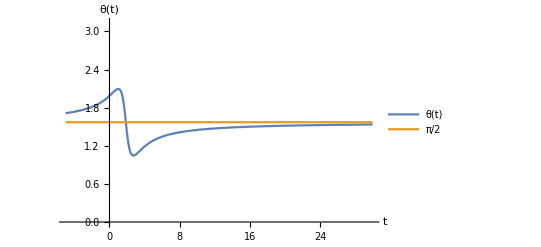

iii) Plotting the speed from t = 0 to t = 6

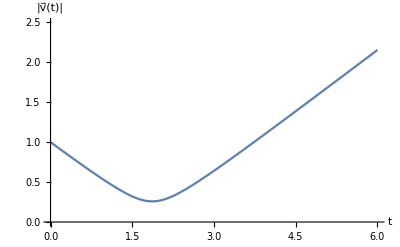

iv) Plotting the particle trajectory from t = 0 to t = 6

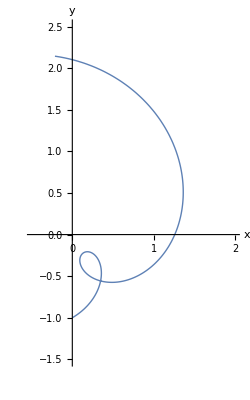

Just for fun again let's look at the long term behavior of the particle:

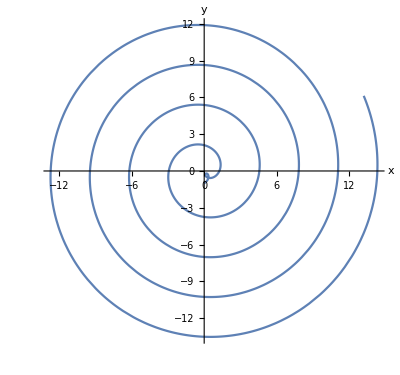

All done!

```mathematica
(* 8 *)
Remove["Global`*"]
Print[Style["8) Particle in Two Dimensions",16,Bold,Red]]
(* i *)
Print[Style["\ni) Velocity, acceleration, and speed from position function",Bold]]
(* Defining r[t] *)
r[t_] = {Sin[t] - t Cos[t] + t Cos[t+π/6],t Sin[t+π/6]-t Sin[t]-Cos[t]};
(* Find velocity, acceleration and speed *)
vel[t_]=r'[t];
acc[t_] = r''[t];
speed[t_]=√(vel[t].vel[t]);
accmag[t] = √(acc[t].acc[t]);
Print["r⃗(t) = ",r[t]//MatrixForm]
Print["v⃗(t) = ",vel[t]//MatrixForm]
Print["a⃗(t) = ",acc[t]//MatrixForm]
Print["|v⃗(t)| = ",speed[t]//FullSimplify]
(* ii *)
(* Angle between acceleration and velocity *)
Print[Style["\nii) Angle between acceleration and velocity",Bold]]
Print["For two vectors a and b, a·b = |a||b|Cos[θ]"]
Print["So θ = ArcCos[(a·b)/(|a || b|)],  and for the angle between a⃗(t) and v⃗(t):"]
θ[t_] = ArcCos[(vel[t].acc[t])/(speed[t] accmag[t])];
Print["θ(t) = ",θ[t]//FullSimplify]
Print["θ(3) = ",θ[3]//N," = ",θ[3]/π//N," π"]
Print["Just for fun let's plot θ[t]:"]
Print[Plot[{θ[t],π/2},{t,-5,30},AxesLabel->{"t","θ(t)"},PlotRange -> {{-5,30},{0,π}},PlotLegends->"Expressions"]]
(* iii *)
Print[Style["\niii) Plotting the speed from t = 0 to t = 6",Bold]]
Print[Plot[speed[t],{t,0,6},AxesLabel->{"t","|v⃗(t)|"},PlotRange -> {{0,6},{0,2.5}}]]
(* iv *)
Print[Style["\niv) Plotting the particle trajectory from t = 0 to t = 6",Bold]]
Print[ParametricPlot[r[t],{t,0,6},PlotStyle->Thick,AxesLabel->{"x","y"},PlotRange->{{-0.5,2},{-1.5,2.5}}]]
Print["Just for fun again let's look at the long term behavior of the particle:"]
Print[ParametricPlot[r[t],{t,0,30},AxesLabel->{"x","y"}]]
Print["All done!"]
```